# Twine HTML Parser

```mathematica
Clear[generateEdges]
generateEdges[parentName_, links_]:= Thread[DirectedEdge[parentName, links]]
Clear[extractLinks]
extractLinks[passageContent_]:=DeleteCases[StringCases[passageContent,("[["~~ShortestMatch[p___]~~"]]"):> p], {}]
```

### Display

```mathematica
Clear[twineParserDisplay]
twineParserDisplay[absoluteFilePath_String]:=Module[{fileAsString,xmlObject, rootNode,rootNodeName, passages,passageContentThread,passageAssociation,edges,alledges, g, v},
(*Import Twine Project as string*)
fileAsString = Import[absoluteFilePath, "String"];

(*Explicitly Parse XML | Riccardo's Algorithm*)
xmlObject = parseXML[fileAsString];

(*Get the root node*)
rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];

(*Extract the Story name*)
rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;

(*Extract the passages in the form {passage-name, content}*)
passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];

(*Create Assocation between passage and content for tooltips and remove the link syntax*)
passageContentThread= AssociationThread[Transpose[passages]⟦1⟧ -> StringReplace[Transpose[passages]⟦2⟧, ("[["~~ShortestMatch[p___]~~"]]"):> p]];

(*AssociationThread[Transpose[passages]⟦1⟧ -> Transpose[passages]⟦2⟧];*)
(*Add rootnode pair to association*)
passageAssociation =AssociateTo[passageContentThread, rootNodeName -> "Start Here"];

(*Extract Links*)
links= DeleteCases[extractLinks[#⟦2⟧]&/@passages, {}];

(*generate edges*)
edges =generatedEdges[#⟦1⟧, extractLinks[#⟦2⟧]]&/@passages;

(*create complete list of edges for graph*)
alledges= Flatten[{{rootNodeName -> First[passages]⟦1⟧},DeleteCases[edges, {}]}];

(*Generate Graph*)
g =Graph[alledges];

(*Generate Tooltips on the graph*)
v =Table[Tooltip[VertexList[g]⟦i⟧, passageAssociation[VertexList[g]⟦i⟧]], {i, 1, Length[VertexList[g]]}];

(*Display graph with tooltips *)
completeGraph = Graph[v, alledges, VertexLabels->"Name",GraphLayout ->{"LayeredDigraphEmbedding", "RootVertex"->rootNodeName}
]
]
twineParserDisplay::usage = "twineParser[path/to/file.html] Displays a graph of a Twine 2 project";
```

```mathematica
?twineParserDisplay
```

twineParser[path/to/file.html] Displays a graph of a Twine 2 project

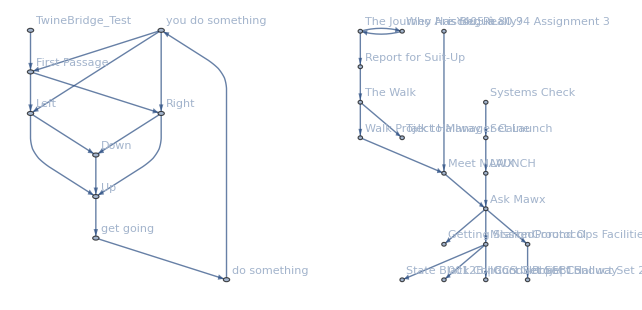

```mathematica
test=twineParserDisplay["~/Documents/Twine/Stories/TwineBridge_Test.html"];
test2 = twineParserDisplay["~/Documents/Twine/Stories/isc405 _ Assignment 3.html"];
GraphicsRow[{test, test2}]
```

### Association Form

```mathematica
Clear[twineToAssociation]
twineToAssociation[absoluteFilePath_String]:=Module[{fileAsString,xmlObject, rootNode,rootNodeName, passages,passageContentThread,passageAssociation,edges,alledges, g, v},
(*Import Twine Project as string*)
fileAsString = Import[absoluteFilePath, "String"];

(*Explicitly Parse XML | Riccardo's Algorithm*)
xmlObject = parseXML[fileAsString];

(*Get the root node*)
rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];

(*Extract the Story name*)
rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;

(*Extract the passages in the form {passage-name, content}*)
passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];

(*Create Assocation between passage and content for tooltips and remove the link syntax*)
passageContentThread= AssociationThread[Transpose[passages]⟦1⟧ -> Transpose[passages]⟦2⟧];
(*Root Node Association*)
rootAssociation = <|rootNodeName -> "Start Here"|>;
(*Add rootnode pair to association*)
passageAssociation =AssociateTo[rootAssociation,passageContentThread]
]
twineToAssociation::usage = "twineToAssociation[path/to/file.html] Generates an Assocation of a Twine 2 project";
```

```mathematica
?twineToAssociation
```

twineParser[path/to/file.html] Generates an Assocation of a Twine 2 project

```mathematica
test=twineToAssociation["~/Documents/Twine/Stories/TwineBridge_Test.html"]
```

<|TwineBridge_Test→Start Here,First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>